```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\Critical-region\QCD\v1\delta\source

```mathematica
c01=Flatten[Import["c0data1.dat"]];
c02=Flatten[Import["c0data2.dat"]];
sigma1=Flatten[Import["sigmadata1.dat"]];
sigma2=Flatten[Import["sigmadata2.dat"]];
csigmabar3=Flatten[{c01,c02}/(3.6*10^9)];
deltalbar3=Flatten[{sigma1,sigma2}/0.0153709];
mpi=Flatten[Import["mpi.dat"]];
LMax=Length[mpi];
```

```mathematica
δO4=SetPrecision[4.792,20];θHO4=SetPrecision[0.29,20];
Clear[ListΔmπ,ListΔc3];ListΔc3[iMin_,iMax_]:=Table[{csigmabar3[[i]],deltalbar3[[i]]},{i,iMin,iMax}]
```

```mathematica
delta43=4.7842049914123224184691716988644852126802550618815156961252`40.;
```

```mathematica
tempfitfab3=;
```

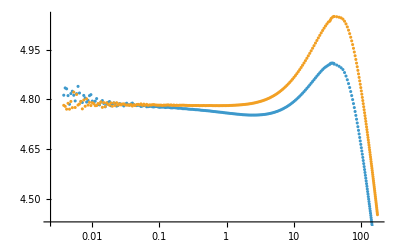

```mathematica
tempfitfab3n2=Block[{Bc12,am12,thetaH=0.272`40},{Bc12,am12}={Bc,am}/.NonlinearModelFit[{Transpose[(SetPrecision[ListΔc3[31,75],80]//Log)][[1]],Transpose[(SetPrecision[ListΔc3[31,75],80]//Log)][[2]]}//Transpose,lgbc+Log[1+am ⅇ^(lgx thetaH)]+lgx/delta43,{lgbc,am},lgx,MaxIterations->400]["BestFitParameters"];ParallelTable[Clear[cfa,cfb,na,nb,xadata,xbdata,yadata,ybdata];
{1/invδ,am12,mpi[[i]]}/.NonlinearModelFit[Transpose[{csigmabar3[[i-4;;i+4]]//Log,(SetPrecision[deltalbar3[[i-4;;i+4]],80]//Log)-Log[1+am12 ⅇ^(Log[SetPrecision[csigmabar3,80]] thetaH)][[i-4;;i+4]]}],lgx*invδ+lgbc,{lgbc,invδ},lgx,MaxIterations->400]["BestFitParameters"],{i,11,280,1}]];
ListPlot[{tempfitfab3[[All,{3,1}]],tempfitfab3n2[[All,{3,1}]]},ScalingFunctions->{"Log",Automatic}]
```